```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["VariationalMethods`"]
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
```

```mathematica
ClearAll[Sd,γm,γp,q2SolDEL,h,k,m,r,q0,v0,q1,q2,qrecursive,σRK]
```

```mathematica
(*k=0;*)
```

```mathematica
(* r=0;*)
```

### Definition of the continuous Lagrangian and Rayleigh potential

```mathematica
L[q_,v_]:=1/2*v^2
```

```mathematica
R[q_,v_]:=1/3*r*v^3
```

```mathematica
f[q_,v_]=-D[R[q,v],v]
```

-r v^2

### Midpoint discrete Lagrangians and Rayleigh potential

```mathematica
(*Ld[q0_,q1_]:=1/2*m*((q1-q0)/h)^2-1/2*k*((q1+q0)/2)^2*)
```

```mathematica
(*Rd[q0_,q1_]:=1/2*r*((q1-q0)/h)^2*)
```

```mathematica
Ld[q0_,q1_]=h*L[(q0+q1)/2,(q1-q0)/h]
```

(-q0+q1)^2/(2 h)

```mathematica
Rd[q0_,q1_]=h^2/2*R[(q0+q1)/2,(q1-q0)/h]
```

((-q0+q1)^3 r)/(6 h)

```mathematica
Ldp[q0_,q1_]=Ld[q0,q1]+Rd[q0,q1]
```

(-q0+q1)^2/(2 h)+((-q0+q1)^3 r)/(6 h)

```mathematica
Ldm[q0_,q1_]=Ld[q0,q1]-Rd[q0,q1]
```

(-q0+q1)^2/(2 h)-((-q0+q1)^3 r)/(6 h)

```mathematica
fdp[q0_,q1_]=h/2*f[(q0+q1)/2,(q1-q0)/h]
```

-((-q0+q1)^2 r)/(2 h)

```mathematica
fdm[q0_,q1_]=h/2*f[(q0+q1)/2,(q1-q0)/h];
```

```mathematica
fdp[q0,q1]==-D[Rd[q0,q1],q1]&&fdm[q0,q1]==D[Rd[q0,q1],q0]//Simplify
```

True

### Discrete Euler-Lagrange equations

```mathematica
DEL:=D[Ldm[Q0,Q1],Q1]+D[Ldp[Q1,Q2],Q1]==0
```

```mathematica
solsDEL=Solve[DEL,Q2]
```

{{Q2→(-1+Q1 r-√(1-2 Q0 r+2 Q1 r-Q0^2 r^2+2 Q0 Q1 r^2-Q1^2 r^2))/r},{Q2→(-1+Q1 r+√(1-2 Q0 r+2 Q1 r-Q0^2 r^2+2 Q0 Q1 r^2-Q1^2 r^2))/r}}

```mathematica
q2SolDEL[q0_,q1_]:=solsDEL[[2,1,2]]/.Q0->q0/.Q1->q1
```

```mathematica
q2SolDELminus[q0_,q1_]:=solsDEL[[1,1,2]]/.Q0->q0/.Q1->q1
```

```mathematica
q2SolDEL[q1,q2]
```

(-1+q2 r+√(1-2 q1 r+2 q2 r-q1^2 r^2+2 q1 q2 r^2-q2^2 r^2))/r

### Continuous Euler-Lagrange equations

```mathematica
ELeq:=VariationalD[L[Q[t],Q'[t]],Q[t],t]+f[Q[t],Q'[t]]==0
```

```mathematica
SolsELeq=First@DSolve[{ELeq,Q[0]==q0,Q'[0]==v0},Q[t],t];
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -1-v0 1 == 0.

```mathematica
σ[t_]=SolsELeq[[1]][[2]]//Simplify
```

(q0 r+Log[r t+1/v0]-Log[1/v0])/r

```mathematica
(*σ[0]==q0&&σ[h]==q1//Simplify*)
```

```mathematica
σ[0]==q0&&σ'[0]==v0//Simplify
```

True

Function of r so that we can play with the parameter

```mathematica
Σ[t_,r_]=SolsELeq[[1]][[2]];
```

Energy

```mathematica
EL[q_,v_]=v*D[L[q,v],v]-L[q,v];
```

```mathematica
Energy[t_]=EL[σ[t],σ'[t]]//Simplify;
```

Give values to the constants before plotting

```mathematica
{h=.25,k=1,m=1,r=.5,q0=0,v0=1};
```

```mathematica
q1=Re[σ[h]]
```

0.235566

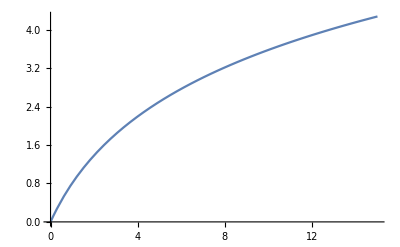

```mathematica
Plot[σ[t],{t,0,15}]
```

```mathematica
Manipulate[Plot[Σ[t,r],{t,0,15}],{r,0.0015,5}]
```

### Runge-Kutta method

```mathematica
(*SolsRungeKutta=NDSolve[{ELeq,Q[0]==q0,Q'[0]==v0},Q[t],{t,0,tend},
StartingStepSize->h,Method->{"FixedStep",Method->{"ExplicitRungeKutta"}}];*)
```

```mathematica
(*σRK[t_]=SolsRungeKutta[[1]][[1]][[2]]*)
```

```mathematica
tend=100;
```

```mathematica
RKsols=Reap[NDSolve[{ELeq,WhenEvent[Mod[t,h]==0,Sow[Q[t]]],Q[0]==q0,Q'[0]==v0},{},{t,tend},Method->{"FixedStep",Method->{"ExplicitRungeKutta"}},StartingStepSize->h]][[-1,1]];
```

```mathematica
RKpts=Table[{h*n,RKsols[[n]]},{n,0,Floor[tend/h]}];
```

```mathematica
Eulersols=Reap[NDSolve[{ELeq,WhenEvent[Mod[t,h]==0,Sow[Q[t]]],Q[0]==q0,Q'[0]==v0},{},{t,tend},Method->{"FixedStep",Method->{"ExplicitEuler"}},StartingStepSize->h]][[-1,1]];
```

```mathematica
Eulerpts=Table[{h*n,Eulersols[[n]]},{n,0,Floor[tend/h]}];
```

```mathematica
(*SolsEuler=First@NDSolve[{ELeq,Q[0]==q0,Q'[0]==v0},Q[t],{t,0,tend},StartingStepSize->h,Method->{"FixedStep",Method->{"ExplicitEuler"
}}];*)
```

```mathematica
(*σEuler[t_]=SolsEuler[[1]][[2]]//Simplify;*)
```

### Continuous vs discrete

```mathematica
qrecursive[0]=q0;
qrecursive[1]=q1;
qrecursive[n_]:=qrecursive[n]=q2SolDEL[qrecursive[n-2],qrecursive[n-1]]
```

```mathematica
qrecursiveminus[0]=q0;
qrecursiveminus[1]=q1;
qrecursiveminus[n_]:=qrecursiveminus[n]=q2SolDELminus[qrecursive[n-2],qrecursive[n-1]]
```

```mathematica
discretepts=Table[{h*n,qrecursive[n]},{n,0,Floor[tend/h]}];
```

```mathematica
discretepts[[2]]=={h,Re[σ[h]]}
```

True

```mathematica
discreteminuspts=Table[{h*n,qrecursiveminus[n]},{n,0,Floor[tend/h]}];
```

```mathematica
discretevels=Table[{(discretepts[[n+1,2]]+discretepts[[n,2]])/2,(discretepts[[n+1,2]]-discretepts[[n,2]])/h},{n,1,100}];
```

```mathematica
RKvels=Table[{(RKpts[[n+1,2]]+RKpts[[n,2]])/2,(RKpts[[n+1,2]]-RKpts[[n,2]])/h},{n,1,100}];
```

```mathematica
Eulervels=Table[{(Eulerpts[[n+1,2]]+Eulerpts[[n,2]])/2,(Eulerpts[[n+1,2]]-Eulerpts[[n,2]])/h},{n,1,100}];
```

```mathematica
(*tend=15;*)
```

```mathematica
tendsmall=15;
```

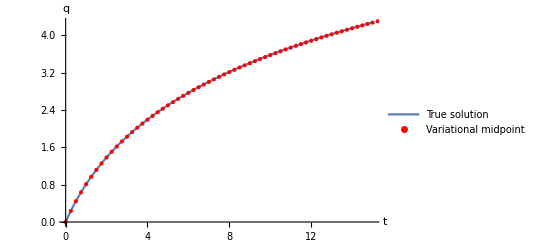

```mathematica
plot=Show[Plot[σ[t],{t,0,tendsmall},PlotLegends->Placed[{"True solution"},Above]],ListPlot[Legended[discretepts,Placed["Variational midpoint",Above]],PlotStyle->Red],
(*ListPlot[Legended[discreteminuspts,Placed["Variational midpoint minus",Above]],PlotStyle->Purple],*)
(*ListPlot[Legended[RKpts,Placed["Runge-Kutta",Above]],PlotStyle->Orange],
ListPlot[Legended[Eulerpts, Placed["Euler method",Above]],PlotStyle->Green],*)
(*PlotRange->{{0,tendsmall},{-.5,.8}}, *)
AxesLabel->{"t","q"}]
```

```mathematica
scale[x_]:=5*x;
```

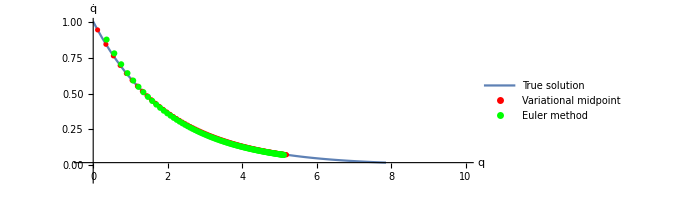

```mathematica
phasespace=Show[
ParametricPlot[{σ[t],σ'[t]},{t,0,tend},
PlotLegends->Placed[{"True solution"},Above]],
ListPlot[Legended[discretevels,Placed["Variational midpoint",Above]],PlotStyle->Red],
(*ListPlot[Legended[RKvels,Placed["Runge-Kutta",Above]],PlotStyle->Orange],*)
ListPlot[Legended[Eulervels, Placed["Euler method",Above]],PlotStyle->Green],
PlotRange->{{-.3,10},{-.1,1}},
(*PlotRange->{{-.3,10},{-.3,5}},*)
AxesLabel->{"q","q̇"}
]
```

```mathematica
Export["./harmonic_oscillator_phase_space.pdf",phasespace];
```

```mathematica
Export["./harmonic_oscillator_plot.pdf",plot];
```

```mathematica
Conservedquantity[q_,v_]=Exp[r*q]*v;
```

```mathematica
Momenta[t_]=Conservedquantity[q,v]/.q->σ[t]/.v->σ'[t]
```

(1. ⅇ^(1. (0.+Log[1+0.5 t])))/(1+0.5 t)

```mathematica
Momentapts=Table[{h*n,Conservedquantity[1/2(discretepts[[n]][[2]]+discretepts[[n-1]][[2]]),1/h(discretepts[[n]][[2]]-discretepts[[n-1]][[2]])]},{n,2,Floor[tend/h]}];
```

```mathematica
MomentaEulerpts=Table[{h*n,Conservedquantity[1/2(Eulerpts[[n]][[2]]+Eulerpts[[n-1]][[2]]),1/h(Eulerpts[[n]][[2]]-Eulerpts[[n-1]][[2]])]},{n,2,Floor[tend/h]}];
```

```mathematica
MomentaRKpts=Table[{h*n,Conservedquantity[1/2(RKpts[[n]][[2]]+RKpts[[n-1]][[2]]),1/h(RKpts[[n]][[2]]-RKpts[[n-1]][[2]])]},{n,2,Floor[tend/h]}];
```

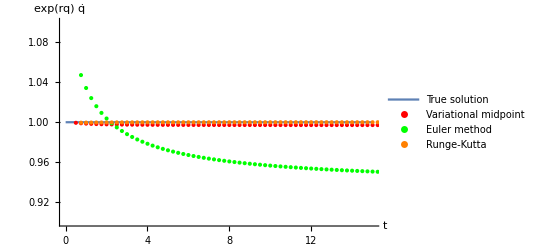

```mathematica
momenta=Show[Plot[Momenta[t],{t,0,tendsmall},PlotLegends->Placed[{"True solution"},Above]],
ListPlot[Legended[Momentapts,Placed["Variational midpoint",Above]],PlotStyle->Red],
ListPlot[Legended[MomentaEulerpts,Placed["Euler method",Above]],PlotStyle->Green],
ListPlot[Legended[MomentaRKpts,Placed["Runge-Kutta",Above]],PlotStyle->Orange],
PlotRange->{{0,tendsmall},{.9,1.1}},
AxesLabel->{"t","exp(rq) q̇"}]
```

```mathematica
Export["./harmonic_oscillator_momenta.pdf",momenta];
```

```mathematica
(*energypts=Table[{h*n,Hdmimp[qrecursive[n-2],qrecursive[n-1],qrecursive[n]]},{n,2,120}];*)
```

```mathematica
energypts=Table[{h*n,EL[(discretepts[[n]][[2]]+discretepts[[n-1]][[2]])/2,(discretepts[[n]][[2]]-discretepts[[n-1]][[2]])/h]},{n,2,Floor[tend/h]}];
```

```mathematica
energyRKpts=Table[{h*n,EL[(RKsols[[n]]+RKsols[[n-1]])/2,(RKsols[[n]]-RKsols[[n-1]])/h]},{n,2,Floor[tend/h]}];
```

```mathematica
energyEulerpts=Table[{h*n,EL[(Eulersols[[n]]+Eulersols[[n-1]])/2,(Eulersols[[n]]-Eulersols[[n-1]])/h]},{n,2,Floor[tend/h]}];;
```

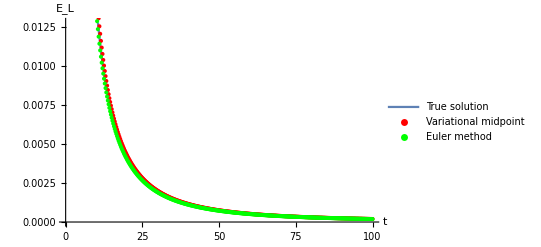

```mathematica
energy=Show[Plot[Energy[t],{t,0,tend},PlotLegends->Placed[{"True solution"},Above]],ListPlot[Legended[energypts,Placed["Variational midpoint",Above]],PlotStyle->Red],
ListPlot[Legended[energyEulerpts, Placed["Euler method",Above]],PlotStyle->Green],
(*ListPlot[Legended[energyRKpts, Placed["Runge-Kutta",Above]],PlotStyle->Orange],*)
(*PlotRange->{{0,tend},Automatic},*)
 AxesLabel->{"t","E_L"}]
```

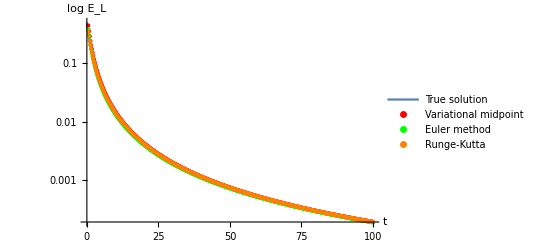

```mathematica
energylog=Show[LogPlot[Energy[t],{t,0,tend},
PlotLegends->Placed[{"True solution"},Above]],
ListLogPlot[Legended[energypts,Placed["Variational midpoint",Above]],PlotStyle->Red],
ListLogPlot[Legended[energyEulerpts, Placed["Euler method",Above]],PlotStyle->Green],
ListLogPlot[Legended[energyRKpts, Placed["Runge-Kutta",Above]],PlotStyle->Orange],
(*PlotRange->{{0,10},Automatic}, *)
(*PlotRange->{{0,100},{-50,0}},*)
AxesLabel->{"t","log E_L"}]
```

```mathematica
Export["./harmonic_oscillator_energy.pdf",energy];
```

```mathematica
Export["./harmonic_oscillator_energy_log.pdf",energylog];
```